{{1.16747,-0.359036,1.10424},{-0.359036,0.378221,0.0586999},{1.10424,0.0586999,1.97974}}

# Orthogonal

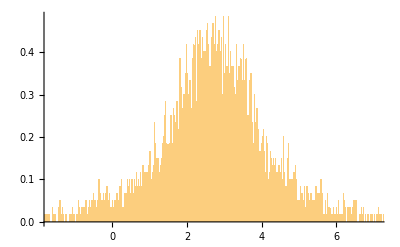

$Aborted

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
$Aborted
```

```mathematica
A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}]//MatrixForm
```

(0.460502 | 0.365167 | 0.678814
-2.6077 | -0.618653 | 0.065228
0.286064 | -0.0609491 | -0.250816
-0.276895 | 0.34143 | -0.787715
-0.301292 | -0.316751 | -0.451454)

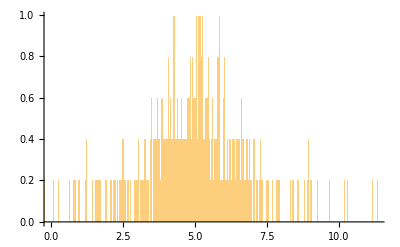

```mathematica
initial =10;
final =10;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[GaussianOrthogonalMatrixDistribution[final]][[1]],{i,1,initial}])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```

## Circular

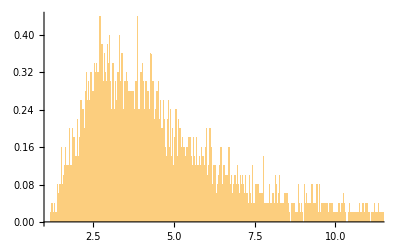

```mathematica
size=3;
Histogram[Table[Log@Sum[(A=RandomVariate[CircularRealMatrixDistribution[size]]^2)[[k,1]]/A[[k,m]],{k,1,Length@A},{m,1,Length@A}],{i,1,5000}],{0.01},"PDF"]
```

## Non-circular

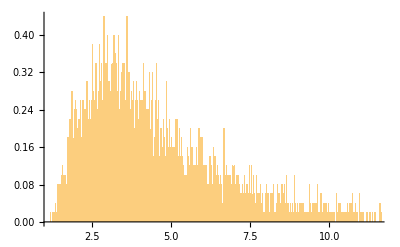

```mathematica
size=3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[size]][[i]],{i,1,size}]^2)[[k,1]]/A[[k,m]],{k,1,Length@A},{m,1,Length@A}],{i,1,5000}],{0.01},"PDF"]
```

## Non-square non-circular

To pierwsze jest poprawne, prawdopodobieństwa stanów początkowych są znormalizowane

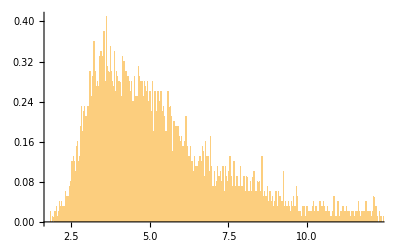

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

A nie prawdopodobieństwa stanów końcowych, jak poniżej

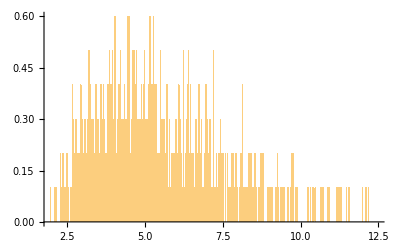

```mathematica
initial =5;
final =3;
Histogram[Table[Log@Sum[(A=Table[RandomVariate[CircularRealMatrixDistribution[final]][[1]]^2,{i,1,initial}]^2)[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```

# Weźmy jeszcze więcej stanów początkowych

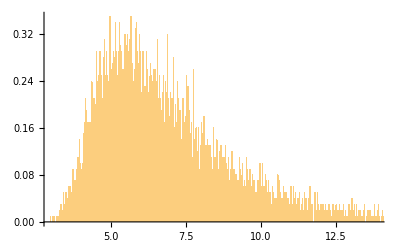

```mathematica
initial =10;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

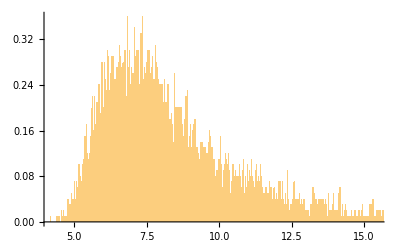

```mathematica
initial =20;
final =3;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

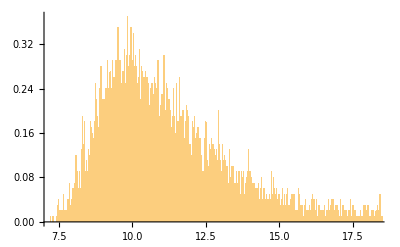

```mathematica
initial =20;
final =10;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

```mathematica
A=RandomVariate[CircularRealMatrixDistribution[3]]
```

{{0.509165,-0.818874,0.264944},{0.422529,0.506012,0.751945},{-0.749813,-0.270918,0.603642}}

```mathematica
Total[A^2]
```

{1.,1.,1.}

```mathematica
A
```

{{0.509165,-0.818874,0.264944},{0.422529,0.506012,0.751945},{-0.749813,-0.270918,0.603642}}

```mathematica
A[[1]]^2
```

{0.259249,0.670555,0.0701955}

# Testing it out

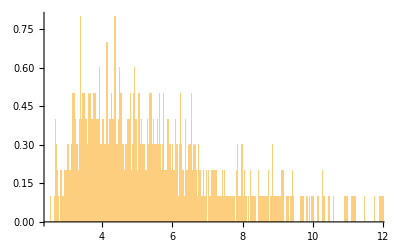

```mathematica
initial =10;
final =2;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```

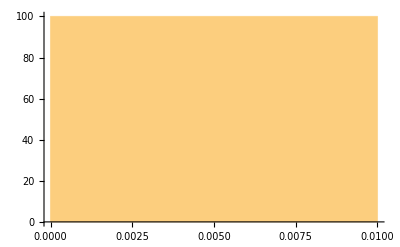

```mathematica
initial =1;
final =1;
Histogram[Table[Log@Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]],{k,1,initial},{m,1,final}],{i,1,10000}],{0.01},"PDF"]
```

```mathematica
sample=RandomVariate[NormalDistribution[2,3],10^3];
```

## Free energy? probably not

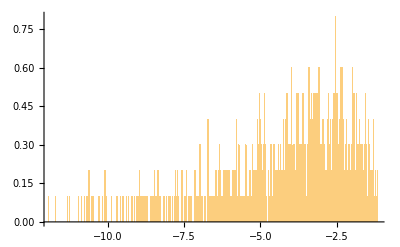

```mathematica
initial =2;
final =2;
Histogram[Table[-Log@ Sum[(A=Transpose[Table[RandomVariate[CircularRealMatrixDistribution[initial]][[1]],{i,1,final}]^2])[[k,1]]/A[[k,m]]/A[[1,1]],{k,1,initial},{m,1,final}],{i,1,1000}],{0.01},"PDF"]
```